# Finding optimal multi-drug combination

In this notebook, we look for optimal multi-drug combinations, which are combinations that maximally affect the PI3K mutant cells while minimizing the effect on WT cells. We will simulate the effect of multi-drug combinations based on network reconstructions in combination with a mapping of the response of ERK and AKT to cell viability. Using these simulations, we will look for 3 or 4 drug combinations (and their concentrations) that minimize the viability of the PI3K mutant cells while keeping the viability of the WT cells above a certain threshold. For proof-of-principle purposes, we’ll also do the reverse.

## Data import, preparation and check

```mathematica
ClearAll["`*"]
$HistoryLength=5;
SetDirectory[NotebookDirectory[]];
(*Functions for plotting the results*)
(*Get["plotting-functions.wl"]*)
SetOptions[SelectedNotebook[],PrintPrecision->6]
```

The network we reconstructed consisted of the following nodes (Note that the order in important to correctly interpret the imported results).

```mathematica
nodes={EGFR,MEK1,ERK1,GSK3,CREB1,BioAkt,PRAS40,P70S6K,RS6};
inhibitors={AKTi,EGFRi,ERKi,GSK3i,IGF1Ri,MEKi,PI3Ki,RAFi,mTORi};
```

Some additional settings.

```mathematica
colWt = RGBColor[152/258,78/258,163/258];
colPi3k = RGBColor[77/258, 175/258, 74/258];
inhibColors=Thread[{mTORi,AKTi,PI3Ki,ERKi,MEKi,RAFi,IGF1Ri,EGFRi}-> ColorData[24,"ColorList"]⟦2;;9⟧]
```

{mTORi→RGBColor[1., 0.7215686274509804, 0.2196078431372549],AKTi→RGBColor[0.9490196078431372, 0.8627450980392157, 0.43529411764705883],PI3Ki→RGBColor[0.6705882352941176, 0.8784313725490196, 0.9372549019607843],ERKi→RGBColor[0.3176470588235294, 0.6549019607843137, 0.7529411764705882],MEKi→RGBColor[0.12941176470588237, 0.5176470588235295, 0.6313725490196078],RAFi→RGBColor[0.09019607843137255, 0.33725490196078434, 0.49411764705882355],IGF1Ri→RGBColor[0.7058823529411765, 0.49411764705882355, 0.5450980392156862],EGFRi→RGBColor[0.5333333333333333, 0.23529411764705882, 0.3058823529411765]}

### Import and check network model

```mathematica
SetDirectory[NotebookDirectory[]];
```

The network reconstructions were obtained in the python notebook "../python/cnr-mcf10a-pi3k.ipynb""../python/cnr-mcf10a-pi3k.ipynb". For convenience we exported a vector directly giving the network response R as function of the applied inhibitor concentrations.

```mathematica
responsePi3k = Thread[nodes-> ToExpression[Import["../results/perturbations/cnr/pi3k_network-response.csv"]]⟦1⟧];
responseWt = Thread[nodes-> ToExpression[Import["../results/perturbations/cnr/wt_network-response.csv"]]⟦1⟧];
```

Example, the first element of the vector gives the response of EGFR as a function of each inhibitor. Of note, inhibitor concentrations are normalized to their IC90. To avoid extrapolation of their effect it should not exceed 1.

```mathematica
responsePi3k⟦1⟧
```

EGFR→-(1.40632 AKTi)/(0.290414+1. AKTi)-(0.857517 EGFRi)/(0.079651+1. EGFRi)-(0.99507 ERKi)/(0.0391414+1. ERKi)-(6.58984 GSK3i)/(100.+1. GSK3i)-(1.55667 MEKi)/(0.783687+1. MEKi)-(31.659 MEKi)/(100.+1. MEKi)-(0.0143309 mTORi)/(0.0442899+1. mTORi)-(13.8678 mTORi)/(22.891+1. mTORi)-(3.13032 PI3Ki)/(11.2417+1. PI3Ki)-(33.4731 RAFi)/(58.4178+1. RAFi)

We’ve also exported the local response matrix and the direct perturbation effects separately. These should be related to the response through the equation R=-r^-1.s. Let’s calculate the difference between these (it should be zero) when we set all inhibitor concentrations to 1.

```mathematica
rlocPi3k = Import["../results/perturbations/cnr/pi3k-rloc.csv"]⟦2;;, 2;;⟧;
sPi3k = ToExpression[Import["../results/perturbations/cnr/pi3k-inhibitor-response.csv"]⟦All, 2⟧];

rlocWt = Import["../results/perturbations/cnr/wt-rloc.csv"]⟦2;;, 2;;⟧;
sWt = ToExpression[Import["../results/perturbations/cnr/wt-inhibitor-response.csv"]⟦All, 2⟧];

(nodes/.responseWt/.Thread[inhibitors->1]) + ( Inverse[rlocWt].sWt/.Thread[inhibitors->1])//Round
(nodes/.responsePi3k/.Thread[inhibitors->1]) + ( Inverse[rlocPi3k].sPi3k/.Thread[inhibitors->1])//Round
```

{0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0}

```mathematica
rlocPi3k//MatrixForm
```

(-1. | 0. | -0.0845823 | 0.942571 | 0. | 0. | 0. | 0. | 0.
1.01787 | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.11823 | -1. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.489287 | -1. | 0. | 0.0562215 | 0. | 0. | 0.
0. | 0. | 0.326992 | 0. | -1. | 0. | 0. | 0. | 0.
0.502892 | 0. | 0. | 0.11496 | 0. | -1. | 2.24217 | 0. | -1.28139
0. | 0. | 0. | 0. | 0. | 0.117684 | -1. | 0. | 0.616463
0. | 0. | 0. | 0. | 0. | 0. | 0.658029 | -1. | 0.
0. | 0. | 0.0319265 | 0. | 0. | 0. | 0. | 0.710012 | -1.)

```mathematica
Clear[rlocPi3k, rlocWt, sWt, sPi3k]
```

### Import parameters mapping signaling to viability

The relation between ERK and AKT response and cell viability was obtain in the Rmarkdown file "../R/perturbations/correlation-signaling-drugresponse.Rmd""../R/perturbations/correlation-signaling-drugresponse.Rmd" . We've used a model 
Viability ~ 1/(1-∆ERK/KM_Erk-∆AKT/KM_AKT) and performed bootstrapping to get robust estimates (using the median estimates of 1000 bootstraps).

```mathematica
Import["../results/perturbations/signaling-viability-parameters.tsv"];
%//TableForm
```

Cell | term | estimate | std.error | statistic | p.value
WT | KM_ERK1 | 0.793069 | 0.16336 | 4.85472 | 0.000037983
WT | KM_BioAkt | 6.0325 | 2.17724 | 2.77072 | 0.00965992
PI3K | KM_ERK1 | 0.976865 | 0.227674 | 4.29063 | 0.000180809
PI3K | KM_BioAkt | 4.53293 | 1.97702 | 2.29281 | 0.0293012

We set the parameters by hand.

```mathematica
paramWt={KMErk1->0.7930688560440792, KMBioAkt->6.032502254687672};
paramPi3k={KMErk1->0.9768651359020766, KMBioAkt->4.53293028600533};
```

We also import the IC10s because we want to restrict each inhibitor to those values.

```mathematica
ToExpression[Import["../results/perturbations/drug-concentrations-annotated.tsv"]];
%//TableForm
(*Add RAFi IC50 manual, using data from pilot experiment, because we only measured single RAFi concentration by accident*)
ic10Norm = {Thread[%%⟦2;;, 1⟧->  %%⟦2;;, -3⟧]}//Flatten;
```

Inhibitor | IC10 | applied_low | IC50 | applied_high | IC90 | IC10_relative | IC50_relative | _relative applied_low
AKTi | 0.278028 | 1 | 2.07086 | 5 | 15.4245 | 0.0556057 | 0.414171 | 0.2
EGFRi | 0.0503414 | 0.3 | 0.374961 | 1 | 2.79285 | 0.0503414 | 0.374961 | 0.3
ERKi | 0.00244322 | 0.02 | 0.018198 | 0.4 | 0.135546 | 0.00610806 | 0.0454951 | 0.05
GSK3i | 3.01772 | 2 | 22.4771 | 5 | 167.418 | 0.603544 | 4.49542 | 0.4
IGF1Ri | 1.16558 | 3 | 8.6817 | 10 | 64.6644 | 0.116558 | 0.86817 | 0.3
MEKi | 0.00033513 | 0.002 | 0.00249617 | 0.02 | 0.0185924 | 0.0167565 | 0.124808 | 0.1
PI3Ki | 0.144145 | 1 | 1.07364 | 2 | 7.99688 | 0.0720724 | 0.536821 | 0.5
mTORi | 0.00350581 | 0.01 | 0.0261125 | 0.3 | 0.194496 | 0.011686 | 0.0870418 | 0.0333333
RAFi | 0.0179633 | 0.15 | 0.133797 | 1 | 0.99657 | 0.0179633 | 0.133797 | 0.15

All concentrations/parameters are relative to the IC90

```mathematica
ic90Norm=Thread[inhibitors->1]
```

{AKTi→1,EGFRi→1,ERKi→1,GSK3i→1,IGF1Ri→1,MEKi→1,PI3Ki→1,RAFi→1,mTORi→1}

## Setting up the functions

### For optimization

Calculate the viability of WT and PI3K cells as function of the applied inhibitor concentrations. We use the cell-line specific parameters relating signaling to viability

```mathematica
viabilityWt=(1/(1-ERK1/KMErk1-BioAkt/KMBioAkt))/.responseWt/.paramWt;

viabilityPi3k=(1/(1-ERK1/KMErk1-BioAkt/KMBioAkt))/. responsePi3k/.paramPi3k

viabilities={wt->viabilityWt, pi3k->viabilityPi3k};
```

1/(1-1.02368 (-(1.60069 AKTi)/(0.290414+1. AKTi)-(0.976036 EGFRi)/(0.079651+1. EGFRi)-(2.51488 ERKi)/(0.0391414+1. ERKi)-(7.50064 GSK3i)/(100.+1. GSK3i)-(3.93424 MEKi)/(0.783687+1. MEKi)-(80.0129 MEKi)/(100.+1. MEKi)-(0.0163116 mTORi)/(0.0442899+1. mTORi)-(15.7845 mTORi)/(22.891+1. mTORi)-(3.56297 PI3Ki)/(11.2417+1. PI3Ki)-(84.5979 RAFi)/(58.4178+1. RAFi))-0.220608 (-(15.1623 AKTi)/(0.290414+1. AKTi)-(0.679545 EGFRi)/(0.079651+1. EGFRi)-(0.904913 ERKi)/(0.0391414+1. ERKi)-(5.8063 GSK3i)/(100.+1. GSK3i)-(1.41563 MEKi)/(0.783687+1. MEKi)-(28.7906 MEKi)/(100.+1. MEKi)-(0.15451 mTORi)/(0.0442899+1. mTORi)-(149.516 mTORi)/(22.891+1. mTORi)-(33.7497 PI3Ki)/(11.2417+1. PI3Ki)-(30.4404 RAFi)/(58.4178+1. RAFi)))

Below, we define the functions to find the optimal concentrations for a given set of inhibitors. We use the FindMinimum function for this, which to finds local minima. However, below we will show that for different starting values, each time the same minimum is found, indicating that there are no local minima in this particular problem,

```mathematica
Clear[optimizeComboPi3k]
optimizeComboPi3k::usage="optimizeComcoPi3k[combo, maxConcentrations, viabilities,  minViabilityWt] finds the concentrations of combo (=List of inhibitor names) that minimizes PI3K mutant viability while ensuring WT viability > minViabilityWt. maxConcentrations is a list of replacementrules that sets the maximum cocentrations of each inhibitor. viabilities is a replacement rule {wt ->.., pi3k->.. } specifying the function relation signaling output to viability. Options to NMimimize can be passed optionally";
optimizeComboPi3k[combo_,maxConcentrations_,viabilities_,minViabilityWt_, opts:OptionsPattern[NMinimize]]:=Module[{
(*Set non-selected inhibitor concentration to 0*)
viabilityComboWt = wt/.viabilities/.Thread[Complement[inhibitors, combo]->0],
viabilityComboPi3k = pi3k/.viabilities/.Thread[Complement[inhibitors, combo]->0]
},
(*Perform the optimization*)
NMinimize[{
(*Function to mimimize*)
viabilityComboPi3k,
 (*Subject to the constraints*)
Thread[0≤combo≤(combo/.maxConcentrations)],(*Drug concentations*)
viabilityComboWt > minViabilityWt  (*WT viability*)
},
combo,
{opts}
]
]
optimizeComboPi3k[{AKTi, EGFRi}, ic10Norm, viabilities, 0.8]
viabilities/.%⟦2⟧/.Thread[inhibitors->0]
```

{0.859228,{AKTi→0.00987207,EGFRi→-1.35832×10^-29}}

{wt→0.8,pi3k→0.859228}

```mathematica
Clear[optimizeComboWt]
optimizeComboWt::usage="optimizeComcoWt[combo, maxConcentrations, minViabilityWt, grouped] finds the concentrations of combo (=List of inhibitor names) that minimizes Wt viability while ensuring Pi3k viability > minViabilityPisk. maxConcentrations is a list of replacementrules that sets the maximum cocentrations of each inhibitor. viabilities is a replacement rule {wt ->.., pi3k->.. } specifying the function relation signaling output to viability. Options to NMimimize can be passed optionally";
optimizeComboWt[combo_,maxConcentrations_,viabilities_,minViabilityPi3k_ ,opts:OptionsPattern[]]:=Module[{
(*Set non-selected inhibitor concentration to 0*)
viabilityComboWt = wt/.viabilities/.Thread[Complement[inhibitors, combo]->0],
viabilityComboPi3k = pi3k/.viabilities/.Thread[Complement[inhibitors, combo]->0]
},
(*Perform the optimization*)
NMinimize[{
viabilityComboWt,
Thread[0≤combo≤(combo/.maxConcentrations)], 
 viabilityComboPi3k > minViabilityPi3k
},
combo,
{opts}
]
]
optimizeComboWt[{AKTi, EGFRi}, ic10Norm, viabilities, 0.8]
viabilities/.%⟦2⟧/.Thread[inhibitors->0]
```

{0.726381,{AKTi→0.00760516,EGFRi→0.00953303}}

{wt→0.726381,pi3k→0.8}

```mathematica
ClearAll[optimizeComboNonsel]
optimizeComboNonsel[combo_,maxConcentrations_,viabilities_,targetViability_, opts:OptionsPattern[NMinimize]]:=Module[{
(*Set non-selected inhibitor concentration to 0*)
viabilityComboWt = wt/.viabilities/.Thread[Complement[inhibitors, combo]->0],
viabilityComboPi3k = pi3k/.viabilities/.Thread[Complement[inhibitors, combo]->0]
},
(*Perform the optimization*)
NMinimize[{
(*Function to mimimize*)
(viabilityComboPi3k-targetViability)^2+(viabilityComboWt-targetViability)^2 ,(*+(viabilityComboWt-viabilityComboPi3k)^2,*)
 (*Subject to the constraints*)
Thread[0≤combo≤(combo/.maxConcentrations)](*Drug concentations*)
(*viabilityComboPi3k<  maxViabilityPi3k  (*WT viability*)*)
},
combo,
{opts}
]
]
Chop[optimizeComboNonsel[inhibitors, ic10Norm, viabilities, 0.8],10^(-5)]
viabilities/.%⟦2⟧/.Thread[inhibitors->0]
```

{0.0000652844,{AKTi→0,EGFRi→0,ERKi→0.000694974,GSK3i→0.603544,IGF1Ri→0,MEKi→0.0167565,PI3Ki→0,RAFi→0.0179633,mTORi→0.00102272}}

{wt→0.795308,pi3k→0.806578}

## Perform the optimization

We’re looking for 3-drug combinations, and use a minimal viability of 0.8 for the cell lines that are not selective. First, we’ll look for combinations that are selective for the PI3K (we don’t expect any clear results). We restrict inhibitor concentrations to be at most their IC10

```mathematica
(*PI3K, IC10*)
(*pi3k3DrugsV80IC10=Table[
optimizeComboPi3k[combo,ic10Norm,viabilities,0.8],
{combo, Subsets[inhibitors, {3}]}(*Scan over all 3-drug combinations*) 
]//Quiet;
Save["../results/perturbations/optimization/pi3k-3dr-ic10.wl",{pi3k3DrugsV80IC10, viabilityPi3k, viabilityWt}]
*)
Get["../results/perturbations/optimization/pi3k-3dr-ic10.wl"];
```

Repeat for WT-selectivity

```mathematica
(*WT, IC10*)
(*wt3DrugsV80IC10=Table[
optimizeComboWt[combo,ic10Norm,viabilities,0.8],
{combo, Subsets[inhibitors, {3}]}(*Scan over all 3-drug combinations*) 
]//Quiet;
Save["../results/perturbations/optimization/wt-3dr-ic10.wl",{wt3DrugsV80IC10, viabilityPi3k, viabilityWt}]
*)
Get["../results/perturbations/optimization/wt-3dr-ic10.wl"];
```

Also get non-selective combinations

```mathematica
(*nonsel3DrugsV80IC10=Table[
optimizeComboNonsel[combo,ic10Norm,viabilities,0.8],
{combo, Subsets[inhibitors, {3}]}(*Scan over all 3-drug combinations*) 
]//Quiet;
Save["../results/perturbations/optimization/nonsel-3dr-ic10.wl",{nonsel3DrugsV80IC10, viabilityPi3k, viabilityWt}]
*)
Get["../results/perturbations/optimization/nonsel-3dr-ic10.wl"];
```

## Select the combinations

```mathematica
drugAnots=ToExpression[Import["../results/perturbations/drug-concentrations-annotated.tsv"]];
drugAnots//TableForm
```

Inhibitor | IC10 | applied_low | IC50 | applied_high | IC90 | IC10_relative | IC50_relative | _relative applied_low
AKTi | 0.278028 | 1 | 2.07086 | 5 | 15.4245 | 0.0556057 | 0.414171 | 0.2
EGFRi | 0.0503414 | 0.3 | 0.374961 | 1 | 2.79285 | 0.0503414 | 0.374961 | 0.3
ERKi | 0.00244322 | 0.02 | 0.018198 | 0.4 | 0.135546 | 0.00610806 | 0.0454951 | 0.05
GSK3i | 3.01772 | 2 | 22.4771 | 5 | 167.418 | 0.603544 | 4.49542 | 0.4
IGF1Ri | 1.16558 | 3 | 8.6817 | 10 | 64.6644 | 0.116558 | 0.86817 | 0.3
MEKi | 0.00033513 | 0.002 | 0.00249617 | 0.02 | 0.0185924 | 0.0167565 | 0.124808 | 0.1
PI3Ki | 0.144145 | 1 | 1.07364 | 2 | 7.99688 | 0.0720724 | 0.536821 | 0.5
mTORi | 0.00350581 | 0.01 | 0.0261125 | 0.3 | 0.194496 | 0.011686 | 0.0870418 | 0.0333333
RAFi | 0.0179633 | 0.15 | 0.133797 | 1 | 0.99657 | 0.0179633 | 0.133797 | 0.15

```mathematica
selectivity=pi3k-wt/.viabilities;
```

Clean the list of optimized combinations.

```mathematica
(*Chop*)
chopEtc[lst_]:=Chop[SetPrecision[lst,2],10^-6]
remove0s[lst_]:={#⟦1⟧,#⟦2⟧/.#⟦2⟧-> DeleteCases[#⟦2⟧,_->0]}&/@lst
wtCleaned=wt3DrugsV80IC10//chopEtc//remove0s//DeleteDuplicates;
pi3kCleaned=pi3k3DrugsV80IC10//chopEtc//remove0s//DeleteDuplicates;
nonselCleaned=nonsel3DrugsV80IC10//chopEtc//remove0s//DeleteDuplicates;
(*Remove all inhibitors that are 0*)
```

Let’s select only combo’s with a predicted selectivity of > 0.1. There are 31 of these, most are 3-drug combinations, but 6 are 2-drug combo’s

```mathematica
wtSelected=Select[wtCleaned,(selectivity/.#⟦2⟧/.Thread[inhibitors->0])>0.1&];
(*Count[Length/@wtSelected⟦All,2⟧,3]
Count[Length/@wtSelected⟦All,2⟧,2]
*)
```

```mathematica
pi3k3DrugsV80IC10//Length
```

84

```mathematica
Select[pi3kCleaned,(selectivity/.#⟦2⟧/.Thread[inhibitors->0])>0.&]
```

{{0.86,{AKTi→0.0099}},{0.84,{EGFRi→0.01,GSK3i→0.6}},{0.85,{EGFRi→0.014}},{0.82,{EGFRi→0.0082,MEKi→0.017}},{0.85,{EGFRi→0.012,RAFi→0.018}},{0.85,{EGFRi→0.014,mTORi→0.0012}},{0.84,{ERKi→0.002,GSK3i→0.6}},{0.82,{ERKi→0.0016,MEKi→0.017}},{0.85,{ERKi→0.0026}},{0.85,{ERKi→0.0023,RAFi→0.018}},{0.85,{ERKi→0.0026,mTORi→0.00078}},{0.85,{AKTi→0.0073,GSK3i→0.6}},{0.82,{AKTi→0.0036,GSK3i→0.6,MEKi→0.017}},{0.84,{AKTi→0.0061,GSK3i→0.6,RAFi→0.018}},{0.85,{AKTi→0.007,GSK3i→0.6,mTORi→0.0014}},{0.83,{AKTi→0.0059,MEKi→0.017}},{0.85,{AKTi→0.0086,RAFi→0.018}},{0.86,{AKTi→0.0097,mTORi→0.00071}},{0.82,{AKTi→0.0048,MEKi→0.017,RAFi→0.018}},{0.83,{AKTi→0.0056,MEKi→0.017,mTORi→0.0018}},{0.85,{AKTi→0.0084,RAFi→0.018,mTORi→0.001}},{0.82,{EGFRi→0.0049,GSK3i→0.6,MEKi→0.017}},{0.84,{EGFRi→0.0084,GSK3i→0.6,RAFi→0.018}},{0.84,{EGFRi→0.0098,GSK3i→0.6,mTORi→0.0012}},{0.82,{EGFRi→0.0066,MEKi→0.017,RAFi→0.018}},{0.82,{EGFRi→0.0079,MEKi→0.017,mTORi→0.0012}},{0.85,{EGFRi→0.012,RAFi→0.018,mTORi→0.0012}},{0.82,{ERKi→0.00097,GSK3i→0.6,MEKi→0.017}},{0.84,{ERKi→0.0016,GSK3i→0.6,RAFi→0.018}},{0.84,{ERKi→0.0019,GSK3i→0.6,mTORi→0.00086}},{0.82,{ERKi→0.0013,MEKi→0.017,RAFi→0.018}},{0.82,{ERKi→0.0016,MEKi→0.017,mTORi→0.00091}},{0.85,{ERKi→0.0022,RAFi→0.018,mTORi→0.00082}},{0.89,{GSK3i→0.6,PI3Ki→0.067}},{0.92,{GSK3i→0.6,IGF1Ri→0.0036,RAFi→0.018}},{0.92,{GSK3i→0.6,mTORi→0.012}},{0.84,{GSK3i→0.6,MEKi→0.017,PI3Ki→0.034}},{0.84,{GSK3i→0.6,MEKi→0.017,mTORi→0.012}},{0.88,{GSK3i→0.6,PI3Ki→0.057,RAFi→0.018}},{0.88,{GSK3i→0.6,PI3Ki→0.045,mTORi→0.012}},{0.89,{GSK3i→0.6,RAFi→0.018,mTORi→0.012}},{0.86,{MEKi→0.017,PI3Ki→0.056}},{0.88,{MEKi→0.017,mTORi→0.012}},{0.91,{PI3Ki→0.072,RAFi→0.018}},{0.91,{PI3Ki→0.066,mTORi→0.012}},{0.94,{IGF1Ri→0.0011,RAFi→0.018,mTORi→0.012}},{0.85,{MEKi→0.017,PI3Ki→0.045,RAFi→0.018}},{0.85,{MEKi→0.017,PI3Ki→0.033,mTORi→0.012}},{0.85,{MEKi→0.017,RAFi→0.018,mTORi→0.012}},{0.89,{PI3Ki→0.056,RAFi→0.018,mTORi→0.012}}}

Let’s visualize the selected combinations. We also export these for plotting (see ...)

```mathematica
inhibsReorderd ={EGFRi,IGF1Ri,RAFi,MEKi,ERKi,GSK3i,PI3Ki,AKTi,mTORi};
```

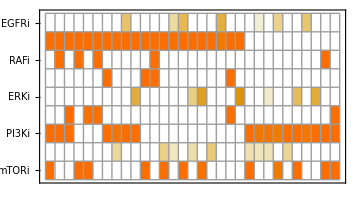

../results/perturbations/optimization/optimization-selected-wtselective-ic10norm.csv

```mathematica
lst=Reverse[Sort[{pi3k-wt/.viabilities/.#/.Thread[inhibitors->0],#}&/@wtSelected[[All,2]]]];
MatrixPlot[
Transpose[inhibsReorderd/(inhibsReorderd/.ic10Norm)/.lst⟦All,2⟧/.Thread[inhibitors->0]],
FrameTicks->{{Array[{#,Style[ToString[inhibsReorderd[[#]]], FontFamily->"Helvetica"],{0,0}}&,{Length[inhibsReorderd]}], None}, {None,None}},
Mesh->True,
ImageSize->Medium
]

Export[
"../results/perturbations/optimization/optimization-selected-wtselective-ic10norm.csv",
Transpose[
Prepend[
Append[inhibsReorderd/(inhibsReorderd/.ic10Norm),selectivity]/.lst⟦All,2⟧/.Thread[inhibitors->0],
Append[inhibsReorderd, "Predicted Selectiviy"]
]
]
]
```

For the non-selective combinations we select those for which the selectivity < 0.1, and that are at least 2-drug-combinations

```mathematica
nonSelMin2=Select[nonselCleaned, Length[#⟦2⟧]≥2&];
nonSelUse=Select[nonSelMin2,(selectivity/.viabilities/.#⟦2⟧/.Thread[inhibitors->0])<0.1&];
nonSelUse//Length
```

44

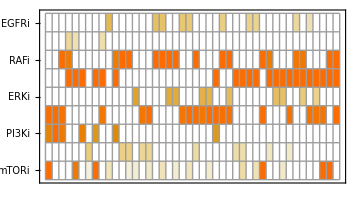

../results/perturbations/optimization/optimization-selected-control-ic10norm.csv

```mathematica
lst=Reverse[Sort[{pi3k-wt/.viabilities/.#/.Thread[inhibitors->0],#}&/@nonSelUse[[All,2]]]];
MatrixPlot[
Transpose[inhibsReorderd/(inhibsReorderd/.ic10Norm)/.lst⟦All,2⟧/.Thread[inhibitors->0]],
FrameTicks->{{Array[{#,Style[ToString[inhibsReorderd[[#]]], FontFamily->"Helvetica"],{0,0}}&,{Length[inhibsReorderd]}], None}, {None,None}},
Mesh->True,
ImageSize->Medium
]
Export[
"../results/perturbations/optimization/optimization-selected-control-ic10norm.csv",
Transpose[
Prepend[
Append[inhibsReorderd/(inhibsReorderd/.ic10Norm),selectivity]/.lst⟦All,2⟧/.Thread[inhibitors->0],
Append[inhibsReorderd, "Predicted Selectiviy"]
]
]
]
```

```mathematica
getAbsoluteConcentrations[combo_]:=Module[
{used=combo⟦All,1⟧,
inhibsReorderd={EGFRi,IGF1Ri,RAFi,MEKi,ERKi,GSK3i,PI3Ki,AKTi,mTORi},
comboNorm
},
comboNorm=SetPrecision[Thread[used ->(used/.combo)*(used/.ic10Norm)],2];
SetPrecision[
Join[
{StringRiffle[StringReplace[ToString[#], " -> "->  ":" ]&/@comboNorm, " + "],
StringRiffle[ToString[#]&/@used, "+"],
Length[used],
wt/.viabilities/.combo/.Thread[inhibsReorderd->0],
pi3k/.viabilities/.combo/.Thread[inhibsReorderd->0],
pi3k-wt/.viabilities/.combo/.Thread[inhibsReorderd->0]
},
inhibsReorderd/.comboNorm/.Thread[inhibsReorderd->0]
],2]
]
```

Export the combinations we will use.

```mathematica
getDF[comboLst_]:=
Join[
{Join[{"AppliedConcentrations","Combo","NDrugs", "WT", "PI3K", "Selectivity"},{EGFRi,IGF1Ri,RAFi,MEKi,ERKi,GSK3i,PI3Ki,AKTi,mTORi}]},
getAbsoluteConcentrations/@comboLst⟦All,2⟧
]
```

```mathematica
Export["../results/perturbations/optimization/optimization-selection-wtselective.tsv",getDF[wtSelected]];
Export["../results/perturbations/optimization/optimization-selection-control.tsv",getDF[nonSelUse]];
```

## Power analysis of the selectivity predictions

To test our method, we will need to compare the selective predictions to a control group. The bottom line of the test is to find a significant difference in selectivity between the combinations predicted to be selective and those that are not. To estimate how many control combinations we need, we’ll here perform a power analysis.  We do this by adding noise to the predictions. From another analysis (see the notebook python/cnr-mcf10a-pi3k.ipynb) we know that the error in viability model fits are roughly normally distributed around 0 with a standard deviation of 0.17. Since this is not cross-validated, we’ll assume an “error-term” with a substantially higher standard deviation of  0.25. 

Note that in this power alalysis we mainly take the error from the prediction into account, not the measurement error of the cell viability. The reason for this is that this is almost neglectable, especially since we perform 8 replicates.

```mathematica
STDEV=0.25;
```

```mathematica
sel=selectivity/.wtSelected⟦All,2⟧/.Thread[inhibitors->0];
nonsel=selectivity/.nonSelUse⟦All,2⟧/.Thread[inhibitors->0];

tmp=Table[MannWhitneyTest[{
Table[x+RandomVariate[NormalDistribution[0, STDEV]],{x,sel}],
Table[x+RandomVariate[NormalDistribution[0,STDEV]],{x,nonsel}]}],{1000}];
Total[#<0.05&/@tmp]
```

100 False+900 True

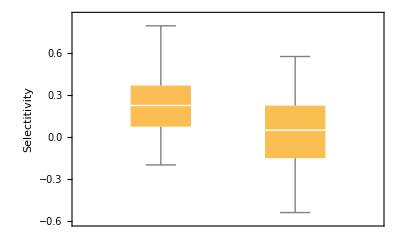

```mathematica
BoxWhiskerChart[{
Table[x+RandomVariate[NormalDistribution[0,STDEV]],{x,sel}],
Table[x+RandomVariate[NormalDistribution[0,STDEV]],{x,nonsel}]},
FrameLabel->{"","Selectitivity"}
]
```